```mathematica
f1=Function[x,Piecewise[{{1,0.3<x<0.7},{0,x<0.3},{0,x>0.7}}]]
```

Function[x,Piecewise[{{1, 0.3<x<0.7}, {0, x<0.3}, {0, x>0.7}}]]

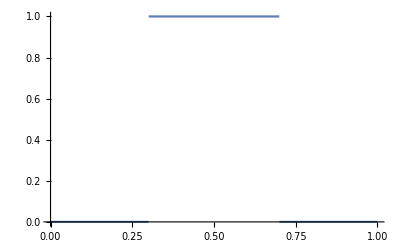

```mathematica
Plot[{f1[x]},{x,0,1}]
```

```mathematica
mode=Function[{n,x},Sin[n π x]]
```

Function[{n,x},Sin[n π x]]

```mathematica
coef= Function[{n,f}, 2*Integrate[f mode[n,x],{x,0,1}]]
```

Function[{n,f},2 ∫_0^1 f mode[n,x]ⅆx]

```mathematica
approxf1=Table[coef[j,f1[x]] mode[j,x],{j,1,100}]
```

{0.748391 Sin[π x],0.,-0.403641 Sin[3 π x],0.,0.,0.,0.172989 Sin[7 π x],0.,-0.0831546 Sin[9 π x],0.,-0.0680356 Sin[11 π x],0.,0.0931479 Sin[13 π x],0.,0.,0.,-0.0712308 Sin[17 π x],0.,0.039389 Sin[19 π x],0.,0.0356377 Sin[21 π x],0.,-0.0526488 Sin[23 π x],0.,0.,0.,0.044849 Sin[27 π x],0.,-0.0258066 Sin[29 π x],0.,-0.0241417 Sin[31 π x],0.,0.0366946 Sin[33 π x],0.,0.,0.,-0.0327276 Sin[37 π x],0.,0.0191895 Sin[39 π x],0.,0.0182534 Sin[41 π x],0.,-0.028161 Sin[43 π x],0.,0.,0.,0.0257643 Sin[47 π x],0.,-0.0152733 Sin[49 π x],0.,-0.0146743 Sin[51 π x],0.,0.0228476 Sin[53 π x],0.,0.,0.,-0.0212443 Sin[57 π x],0.,0.0126846 Sin[59 π x],0.,0.0122687 Sin[61 π x],0.,-0.019221 Sin[63 π x],0.,0.,0.,0.0180735 Sin[67 π x],0.,-0.0108463 Sin[69 π x],0.,-0.0105407 Sin[71 π x],0.,0.016588 Sin[73 π x],0.,0.,0.,-0.0157263 Sin[77 π x],0.,0.00947331 Sin[79 π x],0.,0.0092394 Sin[81 π x],0.,-0.0145894 Sin[83 π x],0.,0.,0.,0.0139187 Sin[87 π x],0.,-0.00840889 Sin[89 π x],0.,-0.00822408 Sin[91 π x],0.,0.0130207 Sin[93 π x],0.,0.,0.,-0.0124837 Sin[97 π x],0.,0.00755951 Sin[99 π x],0.}

```mathematica
Manipulate[Plot[{f1[x],Evaluate[Sum[approxf1[[i]],{i,1,max}]]},{x,0,1}],{max,1,100,1}]
```

```mathematica
f2 = Function[{x,w}, Piecewise[{{x,x<w},{w(1-x)/(1-w),x>w}}]]
```

Function[{x,w},Piecewise[{{x, x<w}, {(w (1-x))/(1-w), x>w}}]]

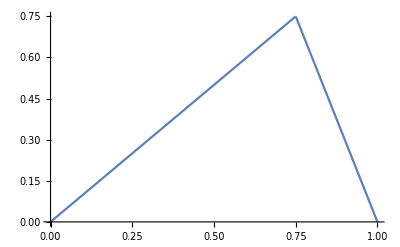

```mathematica
Plot[{f2[x,0.75]},{x,0,1}]
```

```mathematica
2 * Integrate[Sin[π x] * f2[x,0.75], {x,0,1}]
```

0.573159

```mathematica
2 * Integrate[Sin[2π x] * f2[x,0.75], {x,0,1}]
```

-0.202642

```mathematica
approxf2=Table[coef[j,f2[x,0.75]] mode[j,x],{j,1,20}]
```

{0.573159 Sin[π x],-0.202642 Sin[2 π x],0.0636844 Sin[3 π x],0.,-0.0229264 Sin[5 π x],0.0225158 Sin[6 π x],-0.0116971 Sin[7 π x],0.,0.00707604 Sin[9 π x],-0.00810569 Sin[10 π x],0.00473685 Sin[11 π x],0.,-0.00339147 Sin[13 π x],0.00413556 Sin[14 π x],-0.00254737 Sin[15 π x],0.,0.00198325 Sin[17 π x],-0.00250176 Sin[18 π x],0.0015877 Sin[19 π x],0.}

```mathematica
Manipulate[Plot[{f2[x,0.75],Evaluate[Sum[approxf2[[i]],{i,1,max}]]},{x,0,1}],{max,1,20,1}]
```

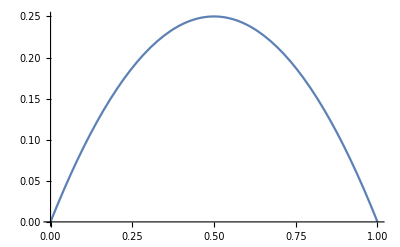

```mathematica
f3=Function[x,-(x-0.5)^2+0.25];
Plot[{f3[x]},{x,0,1}]
```

```mathematica
approxf3=Table[coef[j,f3[x]] mode[j,x],{j,1,20}];
```

```mathematica
Manipulate[Plot[{f3[x],Evaluate[Sum[approxf3[[i]],{i,1,max}]]},{x,0,1}],{max,1,20,1}]
```

```mathematica
f4=Function[x,Piecewise[{{-(x-0.25)^2+0.25^2,x<0.5},{0,x>0.5}}]];
approxf4=Table[coef[j,f4[x]] mode[j,x],{j,1,20}]
Manipulate[Plot[{f4[x],mode[4,x],Evaluate[Sum[approxf4[[i]],{i,1,max}]]},{x,0,1}],{max,1,20,1}]
```

{0.027685 Sin[π x],0.0322515 Sin[2 π x],0.0160359 Sin[3 π x],0.,-0.0030208 Sin[5 π x],0.0011945 Sin[6 π x],0.00244389 Sin[7 π x],0.,-0.00107392 Sin[9 π x],0.000258012 Sin[10 π x],0.000934289 Sin[11 π x],0.,-0.000540814 Sin[13 π x],0.0000940278 Sin[14 π x],0.00048854 Sin[15 π x],0.,-0.000324334 Sin[17 π x],0.0000442408 Sin[18 π x],0.000299476 Sin[19 π x],0.}

```mathematica
freq=Function[{tension,density,n},Sqrt[tension/density] n π]
```

Function[{tension,density,n},√(tension/density) n π]

```mathematica
Animate[Plot[{approxf4[[1]]Cos[freq[1,1,1] t],approxf4[[2]]Cos[freq[1,1,2] t],approxf4[[3]]Cos[freq[1,1,3] t]},{x,0,1},PlotRange->{-0.04,0.04}],{t,0,10}]
```

```mathematica
fullf4 = Evaluate[Sum[approxf4[[i]]Cos[freq[1,1,i] t],{i,1,20}]];
```

```mathematica
Animate[Plot[Evaluate[Sum[approxf4[[i]]Cos[freq[1,1,i] t],{i,1,20}]],{x,0,1},PlotRange->{-0.07,0.07}],{t,0,10}]
```

```mathematica
fullf2 = Evaluate[Sum[approxf2[[i]]Cos[freq[1,1,i] t],{i,1,20}]];
```

```mathematica
Animate[Plot[Evaluate[Sum[approxf2[[i]]Cos[freq[1,1,i] t],{i,1,20}]],{x,0,1},PlotRange->{-0.8,0.8}],{t,0,10}]
```

```mathematica
fullf1 = Evaluate[Sum[approxf1[[i]]Cos[freq[1,1,i] t],{i,1,100}]];
```

```mathematica
Animate[Plot[Evaluate[Sum[approxf1[[i]]Cos[freq[1,1,i] t],{i,1,100}]],{x,0,1},PlotRange->{-1.1,1.1}],{t,0,10}]
```

```mathematica
fullf3 = Evaluate[Sum[approxf3[[i]]Cos[freq[1,1,i] t],{i,1,20}]];
```

```mathematica
Animate[Plot[Evaluate[Sum[approxf3[[i]]Cos[freq[1,1,i] t],{i,1,20}]],{x,0,1},PlotRange->{-0.3,0.3}],{t,0,10}]
```